## Supplement - Resource dynamics parametrization

```mathematica
Quit[];
```

Here we assume a population of N consumer organisms restricted to one habitat patch where one resource is present. The population is monomorphic with respect to the ecological trait x such that all individuals have an attack rate of 1 on the resource. In the following we always assume fast resource dynamics relative to the consumer population dynamics, such that the resource reaches its equilibrium before the organism’s life cycle unfolds. We use the following function for the attack rate of the organism on the resource:

### Chemostat resource dynamics

#### Resource dynamics

The chemostat dynamics represents a typically abiotic resource that flows through the landscape at rate a and is flushed out at rate b. Part of the resource is consumed by the organisms. The dynamics through time is given by the differential equation:

```mathematica
R'[t]==a-(b+N)R[t];
```

Let us visualize the resource dynamics,

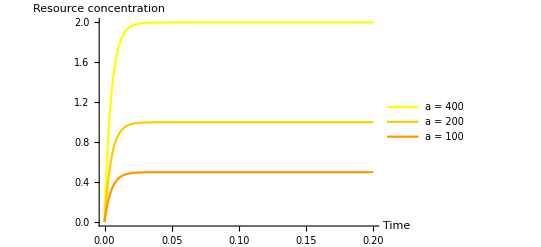
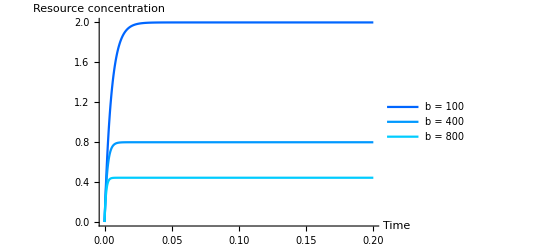
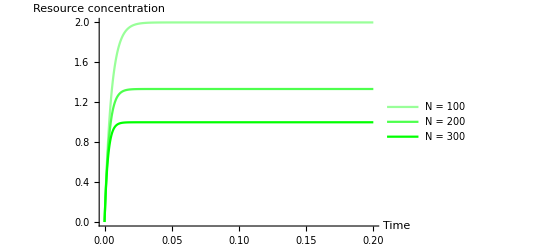

```mathematica
plotChemostat[a0_,b0_,R0_,N0_,T_,plotoptions_]:=Block[{},

(* a is the inflow rate *)
(* b is the outflow rate *)
(* R0 is the initial concentration *)
(* N0 is the consumer population size *)
(* T is the simulation time *)

pars={a->a0,b->b0,N->N0};
ode=R'[t]==a-(b+N)R[t];
sol=NDSolve[{ode/.pars,R[0]==R0},R,{t,0,T}];
Plot[Evaluate[R[t]/.sol],{t,0,T},PlotRange->All,AxesLabel->{"Time","Resource concentration"},plotoptions]
]
p1=plotChemostat[400,100,0.001,100,0.2,{PlotStyle->RGBColor[1,1,0],PlotLegends->LineLegend[{"a = 400"}]}];
p2=plotChemostat[200,100,0.001,100,0.2,{PlotStyle->RGBColor[1,0.8,0],PlotLegends->LineLegend[{"a = 200"}]}];
p3=plotChemostat[100,100,0.001,100,0.2,{PlotStyle->RGBColor[1,0.6,0],PlotLegends->LineLegend[{"a = 100"}]}];
P1=Show[p1,p2,p3];
p1=plotChemostat[400,100,0.001,100,0.2,{PlotStyle->RGBColor[0,0.4,1],PlotLegends->LineLegend[{"b = 100"}]}];
p2=plotChemostat[400,400,0.001,100,0.2,{PlotStyle->RGBColor[0,0.6,1],PlotLegends->LineLegend[{"b = 400"}]}];
p3=plotChemostat[400,800,0.001,100,0.2,{PlotStyle->RGBColor[0,0.8,1],PlotLegends->LineLegend[{"b = 800"}]}];
P2=Show[p1,p2,p3];
p1=plotChemostat[400,100,0.001,100,0.2,{PlotStyle->RGBColor[0.6,1,0.6],PlotLegends->LineLegend[{"N = 100"}]}];
p2=plotChemostat[400,100,0.001,200,0.2,{PlotStyle->RGBColor[0.3,1,0.3],PlotLegends->LineLegend[{"N = 200"}]}];
p3=plotChemostat[400,100,0.001,300,0.2,{PlotStyle->RGBColor[0,1,0],PlotLegends->LineLegend[{"N = 300"}]}];
P3=Show[p1,p2,p3];
{P1,P2,P3}
```

#### Population dynamics

The dynamics of the consumer population are given by

```mathematica
N[t+1]==(1-d+R)N[t];
```

where d is the per capita death rate and R is the equilibrium resource concentration. Assuming fast resource dynamics the equilibrium concentration of the resource is

```mathematica
Solve[a-(b+N)R==0,R]
```

{{R→a/(b+N)}}

We can visualize the dynamics of the consumer population:

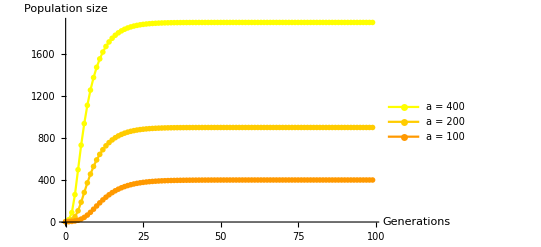
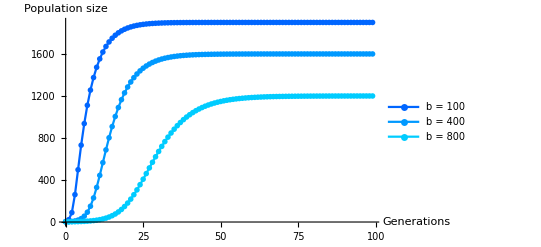
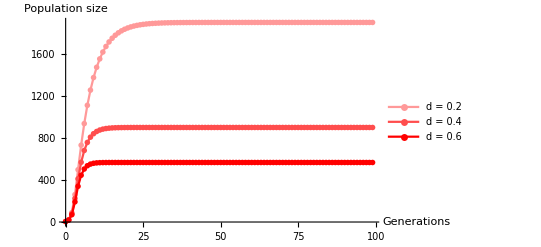

```mathematica
simPopChemostat[a0_,b0_,d0_,N0_,T_,plotoptions_]:=Block[{n=N0,t=0},

(* a0 is the resource inflow rate *)
(* b0 is the resource outflow rate *)
(* d0 is the death rate *)
(* N0 is the initial population size *)
(* T is the simulation time *)

Req=R/.Solve[a-(b+N)R==0,R][[1]];
pop=Reap[While[t<T,
n=(1-d0+R)n /.R->Req/.a->a0/.b->b0/.N->n;
Sow[{t,n}//Flatten];
t=t+1;
]][[2]][[1]];
ListLinePlot[pop,PlotRange->All,AxesLabel->{"Generations","Population size"},plotoptions]
]
p1=simPopChemostat[400,100,0.2,1,100,{PlotStyle->RGBColor[1,1,0],PlotLegends->LineLegend[{"a = 400"}]}];
p2=simPopChemostat[200,100,0.2,1,100,{PlotStyle->RGBColor[1,0.8,0],PlotLegends->LineLegend[{"a = 200"}]}];
p3=simPopChemostat[100,100,0.2,1,100,{PlotStyle->RGBColor[1,0.6,0],PlotLegends->LineLegend[{"a = 100"}]}];
P1=Show[p1,p2,p3];
Export["chemostat_with_different_inflow.pdf",P1,"PDF"];
p1=simPopChemostat[400,100,0.2,1,100,{PlotStyle->RGBColor[0,0.4,1],PlotLegends->LineLegend[{"b = 100"}]}];
p2=simPopChemostat[400,400,0.2,1,100,{PlotStyle->RGBColor[0,0.6,1],PlotLegends->LineLegend[{"b = 400"}]}];
p3=simPopChemostat[400,800,0.2,1,100,{PlotStyle->RGBColor[0,0.8,1],PlotLegends->LineLegend[{"b = 800"}]}];
P2=Show[p1,p2,p3];
Export["chemostat_with_different_outflow.pdf",P2,"PDF"];
p1=simPopChemostat[400,100,0.2,1,100,{PlotStyle->RGBColor[1,0.6,0.6],PlotLegends->LineLegend[{"d = 0.2"}]}];
p2=simPopChemostat[400,100,0.4,1,100,{PlotStyle->RGBColor[1,0.3,0.3],PlotLegends->LineLegend[{"d = 0.4"}]}];
p3=simPopChemostat[400,100,0.6,1,100,{PlotStyle->RGBColor[1,0,0],PlotLegends->LineLegend[{"d = 0.6"}]}];
P3=Show[p1,p2,p3];
Export["chemostat_with_different_death.pdf",P3,"PDF"];
{P1,P2,P3}
```

### Logistic resource dynamics

#### Resource dynamics

In the logistic dynamics, the resource is biotic (e.g. grass or bacteria) and grows even more that it is abundant according to its intrinsic growth rate r, but has a carrying capacity K. The dynamics are:

```mathematica
ode=R'[t]==r(1-R[t]/K)R[t]-N R[t];
```

Let us visualize the resource dynamics,

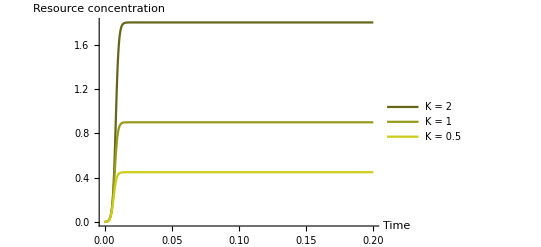
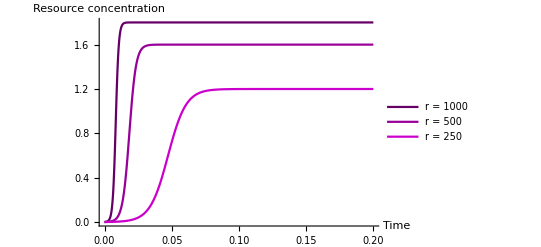
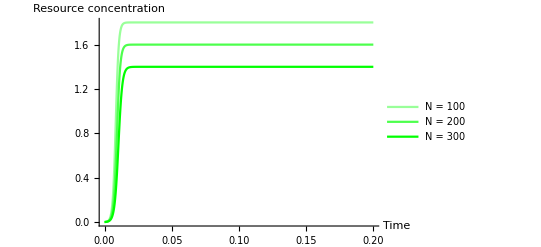

```mathematica
plotLogistic[K0_,r0_,R0_,N0_,T_,plotoptions_]:=Block[{},

(* K is the resource carrying capacity *)
(* r is the intrinsic growth rate of the resource *)
(* R0 is the initial concentration *)
(* N0 is the consumer population size *)
(* T is the simulation time *)

pars={K->K0,r->r0,N->N0};
ode=R'[t]==r(1-R[t]/K)R[t]-N R[t];
sol=NDSolve[{ode/.pars,R[0]==R0},R,{t,0,T}];
Plot[Evaluate[R[t]/.sol],{t,0,T},PlotRange->All,AxesLabel->{"Time","Resource concentration"},plotoptions]
]
p1=plotLogistic[2,1000,0.001,100,0.2,{PlotStyle->RGBColor[0.4,0.4,0.1],PlotLegends->LineLegend[{"K = 2"}]}];
p2=plotLogistic[1,1000,0.001,100,0.2,{PlotStyle->RGBColor[0.6,0.6,0.1],PlotLegends->LineLegend[{"K = 1"}]}];
p3=plotLogistic[0.5,1000,0.001,100,0.2,{PlotStyle->RGBColor[0.8,0.8,0.1],PlotLegends->LineLegend[{"K = 0.5"}]}];
P1=Show[p1,p2,p3];
p1=plotLogistic[2,1000,0.001,100,0.2,{PlotStyle->RGBColor[0.4,0,0.4],PlotLegends->LineLegend[{"r = 1000"}]}];
p2=plotLogistic[2,500,0.001,100,0.2,{PlotStyle->RGBColor[0.6,0,0.6],PlotLegends->LineLegend[{"r = 500"}]}];
p3=plotLogistic[2,250,0.001,100,0.2,{PlotStyle->RGBColor[0.8,0,0.8],PlotLegends->LineLegend[{"r = 250"}]}];
P2=Show[p1,p2,p3];
p1=plotLogistic[2,1000,0.001,100,0.2,{PlotStyle->RGBColor[0.6,1,0.6],PlotLegends->LineLegend[{"N = 100"}]}];
p2=plotLogistic[2,1000,0.001,200,0.2,{PlotStyle->RGBColor[0.3,1,0.3],PlotLegends->LineLegend[{"N = 200"}]}];
p3=plotLogistic[2,1000,0.001,300,0.2,{PlotStyle->RGBColor[0,1,0],PlotLegends->LineLegend[{"N = 300"}]}];
P3=Show[p1,p2,p3];
{P1,P2,P3}
```

#### Population dynamics

Again the dynamics of the consumer population are given by

```mathematica
N[t+1]==(1-d+R)N[t];
```

where the equilibrium resource concentration R is, assuming fast resource dynamics relative to the consumer population dynamics,

```mathematica
Solve[r(1-R/K)R-N R ==0,R]
```

{{R→0},{R→(-K N+K r)/r}}

We can now visualize the dynamics of the consumer population,

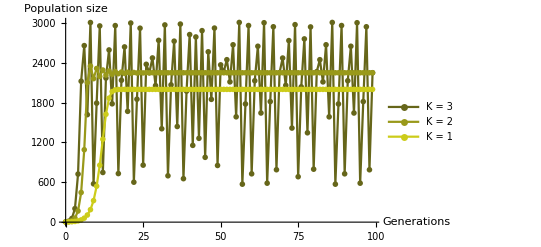
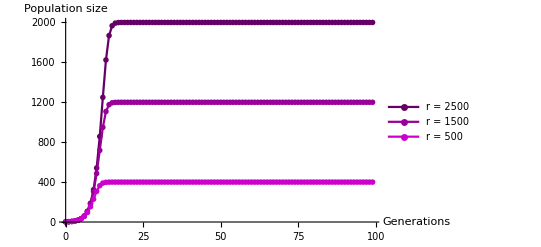
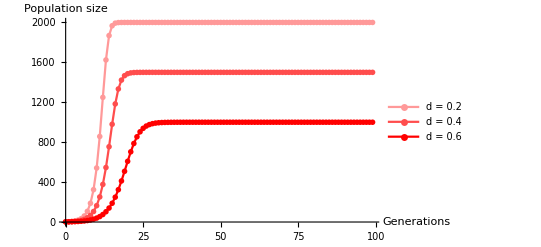

```mathematica
simPopLogistic[K0_,r0_,d0_,N0_,T_,plotoptions_]:=Block[{n=N0,t=0},

(* K0 is the resource carrying capacity *)
(* r0 is the resource intrinsic growth rate *)
(* d0 is the death rate *)
(* N0 is the initial population size *)
(* T is the simulation time *)

Req=R/.Solve[r(1-R/K)R-N R==0,R][[2]];
pop=Reap[While[t<T,
n=(1-d0+R)n /.R->Req/.K->K0/.r->r0/.N->n;
Sow[{t,n}//Flatten];
t=t+1;
]][[2]][[1]];
ListLinePlot[pop,PlotRange->All,AxesLabel->{"Generations","Population size"},plotoptions]
]
p1=simPopLogistic[3,2500,0.2,1,100,{PlotStyle->RGBColor[0.4,0.4,0.1],PlotLegends->LineLegend[{"K = 3"}]}];
p2=simPopLogistic[2,2500,0.2,1,100,{PlotStyle->RGBColor[0.6,0.6,0.1],PlotLegends->LineLegend[{"K = 2"}]}];
p3=simPopLogistic[1,2500,0.2,1,100,{PlotStyle->RGBColor[0.8,0.8,0.1],PlotLegends->LineLegend[{"K = 1"}]}];
P1=Show[p1,p2,p3,PlotRange->All];
Export["logistic_with_different_capacity.pdf",P1,"PDF"];
p1=simPopLogistic[1,2500,0.2,1,100,{PlotStyle->RGBColor[0.4,0,0.4],PlotLegends->LineLegend[{"r = 2500"}]}];
p2=simPopLogistic[1,1500,0.2,1,100,{PlotStyle->RGBColor[0.6,0,0.6],PlotLegends->LineLegend[{"r = 1500"}]}];
p3=simPopLogistic[1,500,0.2,1,100,{PlotStyle->RGBColor[0.8,0,0.8],PlotLegends->LineLegend[{"r = 500"}]}];
P2=Show[p1,p2,p3];
Export["logistic_with_different_growth.pdf",P2,"PDF"];
p1=simPopLogistic[1,2500,0.2,1,100,{PlotStyle->RGBColor[1,0.6,0.6],PlotLegends->LineLegend[{"d = 0.2"}]}];
p2=simPopLogistic[1,2500,0.4,1,100,{PlotStyle->RGBColor[1,0.3,0.3],PlotLegends->LineLegend[{"d = 0.4"}]}];
p3=simPopLogistic[1,2500,0.6,1,100,{PlotStyle->RGBColor[1,0,0],PlotLegends->LineLegend[{"d = 0.6"}]}];
P3=Show[p1,p2,p3];
Export["logistic_with_different_death.pdf",P3,"PDF"];
{P1,P2,P3}
```

### Parametrization

The population dynamics have the same form in the two models:

```mathematica
N[t+1]==(1-d+R)N[t];
```

Whose equilibrium is

```mathematica
Solve[(1-d+R)N==N,{N,R}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{N→0},{R→d}}

The second solution means that the demographic equilibrium is reached when the birth rate (here the equilibrium resource concentration) equals the death rate. This must hold for both types of models. Consider two populations growing, one feeding on an abiotic resource following the chemostat dynamics, and the other feeding on a biotic resource following the logistic dynamics. The population in the chemostat resource model reaches the viable (non-extinct) equilibrium:

```mathematica
N1=Solve[(1-d+R)N==N/.Solve[a-(b+N)R==0,R],N][[2]]
```

{N→(a-b d)/d}

while the population in the logistic resource model reaches the following viable equilibrium:

```mathematica
N2=Solve[(1-d+R)N==N/.Solve[r(1-R/K)R-N R==0,R][[2]],N][[2]]
```

{N→(-d r+K r)/K}

We can therefore find equivalent conditions that lead to the same demographic equilibrium in the two models by substituting parameter values in the following equation and solving it, assuming the death rates are the same in both models:

```mathematica
{N/.N1}=={N/.N2}//Simplify
```

{-b+a/d}=={r-(d r)/K}

For example, if a=400, b=100 and d=0.2 then a logistic resource model with a resource carrying capacity of K=1 will lead the population to the same demographic equilibrium as in the chemostat resource model if the intrinsic growth rate is

```mathematica
Solve[{N/.N1}=={N/.N2} /.a->400/.b->100/.d->0.2/.K->1,r]
```

{{r→2375.}}

We can check that both yield an equilibrium population size of 1900 individuals.

```mathematica
N/.N1/.a->400/.b->100/.d->0.2
N/.N2/.K->1/.r->2375/.d->0.2
```

1900.

1900.

And we can compare the two visually:

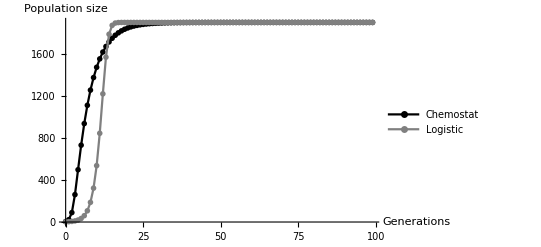

```mathematica
p1=simPopChemostat[400,100,0.2,1,100,{PlotStyle->Black,PlotLegends->LineLegend[{"Chemostat"}]}];
p2=simPopLogistic[1,2375,0.2,1,100,{PlotStyle->Gray,PlotLegends->LineLegend[{"Logistic"}]}];
P=Show[{p1,p2}]
```

```mathematica
Export["/home/raphael/chemostat_vs_logistic.png",P,"PNG", ImageResolution->300];
```